```mathematica
doublebracket[x_]:=If[IntegerQ[x],0,x-Floor[x]-1/2];
s[d_,c_]:=Sum[doublebracket[t/c]*doublebracket[d*t/c],{t,1,c}];
omega[d_,c_]:=Exp[Pi*I*s[d,c]];
Pie[h_,c_]:=If[OddQ[c],ModularInverse[-h,c],ModularInverse[-h,2*c]];
mu[c_,d_,l_,p_]:=Exp[3*Pi*I*c*d*l^2/p^2]*(-1)^(c*l/p+Floor[d*l/p]);
delta16[l_,p_,a_,r_]:=(-1/2-r)*Mod[l*a,p]/p+3/2(Mod[l*a,p]/p)^2+1/24;delta56[l_,p_,a_,r_]:=-5/2*Mod[l*a,p]/p+3/2(Mod[l*a,p]/p)^2+25/24-r+r*Mod[l*a,p]/p;
mmalmod16[almod_,p_,r_]:=(-3 almod^2-p*almod-2*r*p*almod)/2/p^2;
mmalmod56[almod_,p_,r_]:=(-3 almod^2-5*p*almod+2*r*p*almod-2*p^2+2*p^2*r)/2/p^2;
C5[a_,b_]:=N[Cos[a*Pi/5]-Cos[b*Pi/5]];
C7[a_,b_]:=N[Cos[a*Pi/7]-Cos[b*Pi/7]];
(*almod = al-Mod[al,7]*)
```

```mathematica
p=7;NN=49;n=5;(*n=5,12,19... means 7n+5 case*)
For[c=7,c<=NN,c+=7,
If[Mod[c,49]!=0,
graphc={};cc=c/7;
For[r=1,r<=cc,r++,
If[GCD[r,cc]==1,
sd1=0;sd2=0;sd3=0;graphr1={};graphr2={};graphr3={};
For[d=1,d<=c,d++,
If[GCD[d,c]==1&&(Mod[d,cc]==r||cc==1),
a=ModularInverse[d,c];b=(a*d-1)/c;
Pdl1=N[Conjugate[mu[c,d,Mod[a*1,p],p]]/Sin[Pi*Mod[a*1,p]/p]*Exp[-Pi*I*s[d,c]]*Exp[2Pi*I*(n*d)/c]];
sd1+=Pdl1;(*AppendTo[graphr1,Pdl1->Style[StringForm["d_(`1`), d_1 `2`",Mod[d,5],Rationalize[doublebracket[Rationalize[Arg[Pdl1]/2/Pi]-Argl1M1+1/2]]],FontSize->14]]*);
AppendTo[graphr1,Pdl1->Style[StringForm["d_(`1`)=`2`",Mod[d,7],d],FontSize->24]];
Pdl2=N[Conjugate[mu[c,d,Mod[a*2,p],p]]/Sin[Pi*Mod[a*2,p]/p]*Exp[-Pi*I*s[d,c]]*Exp[2Pi*I*(n*d)/c]];
sd2+=Pdl2;(*AppendTo[graphr2,Pdl2->Style[StringForm["d_(`1`), d_1 `2`",Mod[d,5],Rationalize[doublebracket[Rationalize[Arg[Pdl2]/2/Pi]-Argl2M1+1/2]]],FontSize->14]]*);
AppendTo[graphr2,Pdl2->Style[StringForm["d_(`1`)=`2`",Mod[d,7],d],FontSize->24]];
Pdl3=N[Conjugate[mu[c,d,Mod[a*3,p],p]]/Sin[Pi*Mod[a*3,p]/p]*Exp[-Pi*I*s[d,c]]*Exp[2Pi*I*(n*d)/c]];
sd3+=Pdl3;(*AppendTo[graphr2,Pdl2->Style[StringForm["d_(`1`), d_1 `2`",Mod[d,5],Rationalize[doublebracket[Rationalize[Arg[Pdl2]/2/Pi]-Argl2M1+1/2]]],FontSize->14]]*);
AppendTo[graphr3,Pdl3->Style[StringForm["d_(`1`)=`2`",Mod[d,7],d],FontSize->24]];
Print[c," ",r," ",d," ",Pdl1,"  ",Pdl2, "  ",Pdl3,"  ",Rationalize[Arg[Pdl1]/2/Pi]," ",Rationalize[Arg[Pdl2]/2/Pi]," ",Rationalize[Arg[Pdl3]/2/Pi]];
]
];

A=cc;beta=ModularInverse[A,7];betam=ModularInverse[-A,7];
If[beta==1||beta==2||beta==3,
For[sss=0,sss<=6,sss++,If[Mod[r+sss*A,7]==1,Rd1=r+sss*A]];
T=(A*beta-1)/7;
BB=-Rd1*T;
CC=-7*ModularInverse[Rd1,A];
Q1=(-1)^(7*T)*I*Sqrt[7];
Q21=Exp[2*Pi*I*(3/2*T^2+1/2*T)*CC/A];
Q22=Exp[-Pi*I*s[BB,A]];
Q2=Q21*Q22;
Q3=Exp[2*Pi*I*n*BB/A];
Qall=N[Q1*Q2*Q3];
Q1arg=Rationalize[Arg[Q1]/2/Pi];
Q21arg=Rationalize[Arg[Q21]/2/Pi];
Q22arg=Rationalize[Arg[Q22]/2/Pi];
Q2arg=Rationalize[Arg[Q2]/2/Pi];
Q3arg=Rationalize[Arg[Q3]/2/Pi];
Qarg=Rationalize[Arg[Qall]/2/Pi];

If[beta==1,Print[C7[4,6]*Sin[Pi/7]*2*Qall];AppendTo[graphr1,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
If[beta==2,Print[C7[6,2]*Sin[2Pi/7]*2*Qall];AppendTo[graphr2,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];If[beta==3,Print[C7[2,4]*Sin[3Pi/7]*2*Qall];AppendTo[graphr3,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
];

If[betam==1||betam==2||betam==3,
For[sss=0,sss<=6,sss++,If[Mod[r+sss*A,7]==1,Rd1=r+sss*A]];
T=(A*betam+1)/7;
BB=Rd1*T;
CC=-7*ModularInverse[Rd1,A];
Q1=(-1)^(7*T-7)*I*Sqrt[7];
Q21=Exp[2*Pi*I*(3/2*(T-1)^2+5/2*(T-1)+1)*CC/A];
Q22=Exp[-Pi*I*s[BB,A]];
Q2=Q21*Q22;
Q3=Exp[2*Pi*I*n*BB/A];
Qall=N[Q1*Q2*Q3];
Qarg=Rationalize[Arg[Qall]/2/Pi];
If[betam==1,Print[C7[4,6]*Sin[Pi/7]*2*Qall];AppendTo[graphr1,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
If[betam==2,Print[C7[6,2]*Sin[2Pi/7]*2*Qall];AppendTo[graphr2,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];If[betam==3,Print[C7[2,4]*Sin[3Pi/7]*2*Qall];AppendTo[graphr3,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
];

Print[sd1, "  ", sd2,"   ",sd3,"   ",Chop[C7[4,6]*Sin[Pi/7]*sd1+C7[6,2]*Sin[2Pi/7]*sd2+C7[2,4]*Sin[3Pi/7]*sd3]];
;
Print[ComplexListPlot[graphr1,PlotStyle->{PointSize[Large]},PlotMarkers->{Automatic,12},AxesOrigin->{0,0},Ticks->{{{0,"0"}},{{0,"0"}}},LabelStyle->Style[FontFamily->"Times New Roman",FontSize->24],Epilog->{{Red,Circle[{0,0},1/Sin[Pi/p]]},{Red,Circle[{0,0},1/Sin[2*Pi/p]]} ,{Red,Circle[{0,0},1/Sin[3*Pi/p]]} },PlotRange->{{-4,4},{-4,3}},PlotLabel->Style[StringForm["ℓ=1, points for V(`1`,`2`)",r,c],FontSize->24]]];Print[ComplexListPlot[graphr2,PlotStyle->{PointSize[Large]},PlotMarkers->{Automatic,12},AxesOrigin->{0,0},Ticks->{{{0,"0"}},{{0,"0"}}},LabelStyle->Style[FontFamily->"Times New Roman",FontSize->24],Epilog->{{Red,Circle[{0,0},1/Sin[Pi/p]]},{Red,Circle[{0,0},1/Sin[2*Pi/p]]},{Red,Circle[{0,0},1/Sin[3*Pi/p]]}},PlotRange->{{-4,4},{-4,3}},PlotLabel->Style[StringForm["ℓ=2, points for V(`1`,`2`)",r,c],FontSize->24]]];
Print[ComplexListPlot[graphr3,PlotStyle->{PointSize[Large]},PlotMarkers->{Automatic,12},AxesOrigin->{0,0},Ticks->{{{0,"0"}},{{0,"0"}}},LabelStyle->Style[FontFamily->"Times New Roman",FontSize->24],Epilog->{{Red,Circle[{0,0},1/Sin[Pi/p]]},{Red,Circle[{0,0},1/Sin[2*Pi/p]]},{Red,Circle[{0,0},1/Sin[3*Pi/p]]}},PlotRange->{{-4,4},{-4,3}},PlotLabel->Style[StringForm["ℓ=3, points for V(`1`,`2`)",r,c],FontSize->24]]];
]
]
]
]
```

7 1 1 1.-2.07652 ⅈ  -0.554958-1.15238 ⅈ  0.801938+0.639524 ⅈ  -5/28 -9/28 3/28

7 1 2 1.+0.228243 ⅈ  -2.24698+0.512858 ⅈ  -0.554958-1.15238 ⅈ  1/28 13/28 -9/28

7 1 3 -1.-0.797473 ⅈ  -0.801938+0.639524 ⅈ  2.24698+0.512858 ⅈ  -11/28 11/28 1/28

7 1 4 1.-0.797473 ⅈ  0.801938+0.639524 ⅈ  -2.24698+0.512858 ⅈ  -3/28 3/28 13/28

7 1 5 -1.+0.228243 ⅈ  2.24698+0.512858 ⅈ  0.554958-1.15238 ⅈ  13/28 1/28 -5/28

7 1 6 -1.-2.07652 ⅈ  0.554958-1.15238 ⅈ  -0.801938+0.639524 ⅈ  -9/28 -5/28 11/28

0.+1.55765 ⅈ

-2.22045×10^-16-5.2915 ⅈ  2.22045×10^-16+0. ⅈ   0.+3.33067×10^-16 ⅈ   0.-1.55765 ⅈ

-Graphics-

-Graphics-

-Graphics-

14 1 1 -2.24698+0.512858 ⅈ  0.554958+1.15238 ⅈ  1.+0.228243 ⅈ  13/28 5/28 1/28

14 1 3 0.554958-1.15238 ⅈ  0.801938-0.639524 ⅈ  -1.-2.07652 ⅈ  -5/28 -3/28 -9/28

14 1 5 -0.801938+0.639524 ⅈ  -2.24698-0.512858 ⅈ  -1.-0.797473 ⅈ  11/28 -13/28 -11/28

14 1 9 0.801938+0.639524 ⅈ  2.24698-0.512858 ⅈ  1.-0.797473 ⅈ  3/28 -1/28 -3/28

14 1 11 -0.554958-1.15238 ⅈ  -0.801938-0.639524 ⅈ  1.-2.07652 ⅈ  -9/28 -11/28 -5/28

14 1 13 2.24698+0.512858 ⅈ  -0.554958+1.15238 ⅈ  -1.+0.228243 ⅈ  1/28 9/28 13/28

0.+4.36443 ⅈ

0.+6.66134×10^-16 ⅈ  -1.11022×10^-16-6.66134×10^-16 ⅈ   0.-5.2915 ⅈ   0.-4.36443 ⅈ

-Graphics-

-Graphics-

-Graphics-

21 1 1 -1.25044+1.93606 ⅈ  1.0914-0.666941 ⅈ  0.326677+0.972305 ⅈ  43/126 -11/126 25/126

21 1 4 0.893078+0.915628 ⅈ  0.127541-1.01776 ⅈ  1.25044-1.93606 ⅈ  8/63 -29/126 -10/63

21 1 10 1.27269-0.127352 ⅈ  -0.556499+0.861629 ⅈ  -0.286583+2.28688 ⅈ  -1/63 43/126 17/63

21 1 13 0.286583-2.28688 ⅈ  0.40736+1.21244 ⅈ  0.875235-0.534845 ⅈ  -29/126 25/126 -11/126

21 1 16 -0.326677-0.972305 ⅈ  2.29331-0.22948 ⅈ  -0.893078-0.915628 ⅈ  -19/63 -1/63 -47/126

21 1 19 -0.875235+0.534845 ⅈ  1.60927+1.6499 ⅈ  -1.27269+0.127352 ⅈ  26/63 8/63 61/126

5.92644+2.15705 ⅈ

-7.77156×10^-16-2.22045×10^-16 ⅈ  4.97239+1.8098 ⅈ   4.44089×10^-16-1.66533×10^-16 ⅈ   -5.92644-2.15705 ⅈ

-Graphics-

-Graphics-

-Graphics-

21 2 2 0.875235+0.534845 ⅈ  -1.60927+1.6499 ⅈ  1.27269+0.127352 ⅈ  11/126 47/126 1/63

21 2 5 0.326677-0.972305 ⅈ  -2.29331-0.22948 ⅈ  0.893078-0.915628 ⅈ  -25/126 -61/126 -8/63

21 2 8 -0.286583-2.28688 ⅈ  -0.40736+1.21244 ⅈ  -0.875235-0.534845 ⅈ  -17/63 19/63 -26/63

21 2 11 -1.27269-0.127352 ⅈ  0.556499+0.861629 ⅈ  0.286583+2.28688 ⅈ  -61/126 10/63 29/126

21 2 17 -0.893078+0.915628 ⅈ  -0.127541-1.01776 ⅈ  -1.25044-1.93606 ⅈ  47/126 -17/63 -43/126

21 2 20 1.25044+1.93606 ⅈ  -1.0914-0.666941 ⅈ  -0.326677+0.972305 ⅈ  10/63 -26/63 19/63

-5.92644+2.15705 ⅈ

2.22045×10^-16-2.22045×10^-16 ⅈ  -4.97239+1.8098 ⅈ   -9.4369×10^-16-1.11022×10^-16 ⅈ   5.92644-2.15705 ⅈ

-Graphics-

-Graphics-

-Graphics-

28 1 1 -0.386062+2.2722 ⅈ  -0.354086-1.22906 ⅈ  -0.897731+0.496159 ⅈ  31/112 -33/112 47/112

28 1 5 0.283955+0.985629 ⅈ  -2.30114+0.129229 ⅈ  0.852289+0.953712 ⅈ  23/112 55/112 15/112

28 1 9 0.897731-0.496159 ⅈ  -1.53577-1.71853 ⅈ  1.27704-0.0717168 ⅈ  -9/112 -41/112 -1/112

28 1 13 1.3337-1.87968 ⅈ  -1.11945+0.6187 ⅈ  -0.283955-0.985629 ⅈ  -17/112 47/112 -33/112

28 1 17 -0.852289-0.953712 ⅈ  -0.171814+1.01122 ⅈ  -1.3337+1.87968 ⅈ  -41/112 31/112 39/112

28 1 25 -1.27704+0.0717168 ⅈ  0.593553-0.836535 ⅈ  0.386062-2.2722 ⅈ  55/112 -17/112 -25/112

-5.82671-2.4135 ⅈ

2.22045×10^-16-5.41234×10^-16 ⅈ  -4.88871-2.02497 ⅈ   -1.11022×10^-16+4.44089×10^-16 ⅈ   5.82671+2.4135 ⅈ

-Graphics-

-Graphics-

-Graphics-

28 3 3 1.27704+0.0717168 ⅈ  -0.593553-0.836535 ⅈ  -0.386062-2.2722 ⅈ  1/112 -39/112 -31/112

28 3 11 0.852289-0.953712 ⅈ  0.171814+1.01122 ⅈ  1.3337+1.87968 ⅈ  -15/112 25/112 17/112

28 3 15 -1.3337-1.87968 ⅈ  1.11945+0.6187 ⅈ  0.283955-0.985629 ⅈ  -39/112 9/112 -23/112

28 3 19 -0.897731-0.496159 ⅈ  1.53577-1.71853 ⅈ  -1.27704-0.0717168 ⅈ  -47/112 -15/112 -55/112

28 3 23 -0.283955+0.985629 ⅈ  2.30114+0.129229 ⅈ  -0.852289+0.953712 ⅈ  33/112 1/112 41/112

28 3 27 0.386062+2.2722 ⅈ  0.354086-1.22906 ⅈ  0.897731+0.496159 ⅈ  25/112 -23/112 9/112

5.82671-2.4135 ⅈ

-3.33067×10^-16-4.44089×10^-16 ⅈ  4.88871-2.02497 ⅈ   2.22045×10^-16+1.11022×10^-16 ⅈ   -5.82671+2.4135 ⅈ

-Graphics-

-Graphics-

-Graphics-

35 1 1 0.206598+2.29549 ⅈ  -1.26747-0.171691 ⅈ  -0.526089-0.880525 ⅈ  33/140 -67/140 -47/140

35 1 6 -1.18211-1.97852 ⅈ  -0.924489+0.883902 ⅈ  0.0919446+1.02159 ⅈ  -47/140 53/140 33/140

35 1 11 1.26747+0.171691 ⅈ  0.856036+0.565064 ⅈ  1.66587-1.59274 ⅈ  3/140 13/140 -17/140

35 1 16 -0.856036-0.565064 ⅈ  -0.206598-2.29549 ⅈ  0.449425-1.19749 ⅈ  -57/140 -37/140 -27/140

35 1 26 -0.360411+0.960312 ⅈ  1.18211+1.97852 ⅈ  1.06746+0.704624 ⅈ  43/140 23/140 13/140

35 1 31 0.924489-0.883902 ⅈ  0.360411-0.960312 ⅈ  2.28391+0.309376 ⅈ  -17/140 -27/140 3/140

-4.15082+1.34868 ⅈ

-6.66134×10^-16+3.33067×10^-16 ⅈ  -1.11022×10^-16-4.44089×10^-16 ⅈ   5.03252-1.63516 ⅈ   4.15082-1.34868 ⅈ

-Graphics-

-Graphics-

-Graphics-

35 2 2 0.801938-0.639524 ⅈ  2.24698+0.512858 ⅈ  1.+0.797473 ⅈ  -3/28 1/28 3/28

35 2 12 -0.801938-0.639524 ⅈ  -2.24698+0.512858 ⅈ  -1.+0.797473 ⅈ  -11/28 13/28 11/28

35 2 17 0.554958+1.15238 ⅈ  0.801938+0.639524 ⅈ  -1.+2.07652 ⅈ  5/28 3/28 9/28

35 2 22 -2.24698-0.512858 ⅈ  0.554958-1.15238 ⅈ  1.-0.228243 ⅈ  -13/28 -5/28 -1/28

35 2 27 2.24698-0.512858 ⅈ  -0.554958-1.15238 ⅈ  -1.-0.228243 ⅈ  -1/28 -9/28 -13/28

35 2 32 -0.554958+1.15238 ⅈ  -0.801938+0.639524 ⅈ  1.+2.07652 ⅈ  9/28 11/28 5/28

0.-4.36443 ⅈ

-2.22045×10^-16-6.66134×10^-16 ⅈ  3.33067×10^-16+5.55112×10^-16 ⅈ   -3.33067×10^-16+5.2915 ⅈ   0.+4.36443 ⅈ

-Graphics-

-Graphics-

-Graphics-

35 3 3 0.554958+1.15238 ⅈ  0.801938+0.639524 ⅈ  -1.+2.07652 ⅈ  5/28 3/28 9/28

35 3 8 -2.24698-0.512858 ⅈ  0.554958-1.15238 ⅈ  1.-0.228243 ⅈ  -13/28 -5/28 -1/28

35 3 13 2.24698-0.512858 ⅈ  -0.554958-1.15238 ⅈ  -1.-0.228243 ⅈ  -1/28 -9/28 -13/28

35 3 18 -0.554958+1.15238 ⅈ  -0.801938+0.639524 ⅈ  1.+2.07652 ⅈ  9/28 11/28 5/28

35 3 23 0.801938-0.639524 ⅈ  2.24698+0.512858 ⅈ  1.+0.797473 ⅈ  -3/28 1/28 3/28

35 3 33 -0.801938-0.639524 ⅈ  -2.24698+0.512858 ⅈ  -1.+0.797473 ⅈ  -11/28 13/28 11/28

0.-4.36443 ⅈ

-3.33067×10^-16-5.55112×10^-16 ⅈ  4.44089×10^-16+2.22045×10^-16 ⅈ   -4.44089×10^-16+5.2915 ⅈ   0.+4.36443 ⅈ

-Graphics-

-Graphics-

-Graphics-

35 4 4 -0.924489-0.883902 ⅈ  -0.360411-0.960312 ⅈ  -2.28391+0.309376 ⅈ  -53/140 -43/140 67/140

35 4 9 0.360411+0.960312 ⅈ  -1.18211+1.97852 ⅈ  -1.06746+0.704624 ⅈ  27/140 47/140 57/140

35 4 19 0.856036-0.565064 ⅈ  0.206598-2.29549 ⅈ  -0.449425-1.19749 ⅈ  -13/140 -33/140 -43/140

35 4 24 -1.26747+0.171691 ⅈ  -0.856036+0.565064 ⅈ  -1.66587-1.59274 ⅈ  67/140 57/140 -53/140

35 4 29 1.18211-1.97852 ⅈ  0.924489+0.883902 ⅈ  -0.0919446+1.02159 ⅈ  -23/140 17/140 37/140

35 4 34 -0.206598+2.29549 ⅈ  1.26747-0.171691 ⅈ  0.526089-0.880525 ⅈ  37/140 -3/140 -23/140

4.15082+1.34868 ⅈ

-1.94289×10^-16+4.44089×10^-16 ⅈ  2.22045×10^-16-4.996×10^-16 ⅈ   -5.03252-1.63516 ⅈ   -4.15082-1.34868 ⅈ

-Graphics-

-Graphics-

-Graphics-

42 1 1 0.624224+2.21862 ⅈ  -0.746636+1.03851 ⅈ  0.900807-0.490553 ⅈ  13/63 22/63 -5/63

42 1 13 -1.34539+1.87133 ⅈ  0.346418+1.23124 ⅈ  -0.678702-0.769063 ⅈ  22/63 13/63 -23/63

42 1 19 -0.945174-0.398424 ⅈ  2.3019-0.114883 ⅈ  0.346418+1.23124 ⅈ  -55/126 -1/126 13/63

42 1 25 0.846328+0.959006 ⅈ  0.900807-0.490553 ⅈ  -2.12379-0.895251 ⅈ  17/126 -5/63 -55/126

42 1 31 -1.12329+0.61171 ⅈ  -0.678702-0.769063 ⅈ  2.3019-0.114883 ⅈ  53/126 -23/63 -1/126

42 1 37 1.02444-0.0511278 ⅈ  -2.12379-0.895251 ⅈ  -0.746636+1.03851 ⅈ  -1/126 -55/126 22/63

0.270482-1.53398 ⅈ

-0.91886+5.21111 ⅈ  0.+0. ⅈ   0.+2.22045×10^-16 ⅈ   -0.270482+1.53398 ⅈ

-Graphics-

-Graphics-

-Graphics-

42 5 5 -1.02444-0.0511278 ⅈ  2.12379-0.895251 ⅈ  0.746636+1.03851 ⅈ  -31/63 -4/63 19/126

42 5 11 1.12329+0.61171 ⅈ  0.678702-0.769063 ⅈ  -2.3019-0.114883 ⅈ  5/63 -17/126 -31/63

42 5 17 -0.846328+0.959006 ⅈ  -0.900807-0.490553 ⅈ  2.12379-0.895251 ⅈ  23/63 -53/126 -4/63

42 5 23 0.945174-0.398424 ⅈ  -2.3019-0.114883 ⅈ  -0.346418+1.23124 ⅈ  -4/63 -31/63 37/126

42 5 29 1.34539+1.87133 ⅈ  -0.346418+1.23124 ⅈ  0.678702-0.769063 ⅈ  19/126 37/126 -17/126

42 5 41 -0.624224+2.21862 ⅈ  0.746636+1.03851 ⅈ  -0.900807-0.490553 ⅈ  37/126 19/126 -53/126

-0.270482-1.53398 ⅈ

0.91886+5.21111 ⅈ  0.+2.22045×10^-16 ⅈ   1.11022×10^-16+3.33067×10^-16 ⅈ   0.270482+1.53398 ⅈ

-Graphics-

-Graphics-

-Graphics-

49 1 1 1.65563+1.60338 ⅈ  0.918803+0.889811 ⅈ  0.736823+0.713573 ⅈ  6/49 6/49 6/49

49 1 8 -1.9316+1.25733 ⅈ  -1.07195+0.697765 ⅈ  -0.859641+0.559564 ⅈ  20/49 20/49 20/49

49 1 15 -0.795985-2.16295 ⅈ  -0.441738-1.20035 ⅈ  -0.354247-0.962603 ⅈ  -15/49 -15/49 -15/49

49 1 22 2.28584-0.294727 ⅈ  1.26855-0.163561 ⅈ  1.0173-0.131166 ⅈ  -1/49 -1/49 -1/49

49 1 29 -0.22131+2.29411 ⅈ  -0.122818+1.27314 ⅈ  -0.0984924+1.02098 ⅈ  13/49 13/49 13/49

49 1 36 -2.18735-0.72625 ⅈ  -1.21389-0.403039 ⅈ  -0.973462-0.323212 ⅈ  -22/49 -22/49 -22/49

49 1 43 1.19477-1.9709 ⅈ  0.663049-1.09377 ⅈ  0.531724-0.877134 ⅈ  -8/49 -8/49 -8/49

-Graphics-

-Graphics-

-Graphics-

49 2 2 -0.415193-0.937928 ⅈ  -0.93293-2.10751 ⅈ  0.517737+1.16958 ⅈ  -31/98 -31/98 9/49

49 2 9 -0.415193-0.937928 ⅈ  -0.93293-2.10751 ⅈ  0.517737+1.16958 ⅈ  -31/98 -31/98 9/49

49 2 16 -0.415193-0.937928 ⅈ  -0.93293-2.10751 ⅈ  0.517737+1.16958 ⅈ  -31/98 -31/98 9/49

49 2 23 -0.415193-0.937928 ⅈ  -0.93293-2.10751 ⅈ  0.517737+1.16958 ⅈ  -31/98 -31/98 9/49

49 2 30 -0.415193-0.937928 ⅈ  -0.93293-2.10751 ⅈ  0.517737+1.16958 ⅈ  -31/98 -31/98 9/49

49 2 37 -0.415193-0.937928 ⅈ  -0.93293-2.10751 ⅈ  0.517737+1.16958 ⅈ  -31/98 -31/98 9/49

49 2 44 -0.415193-0.937928 ⅈ  -0.93293-2.10751 ⅈ  0.517737+1.16958 ⅈ  -31/98 -31/98 9/49

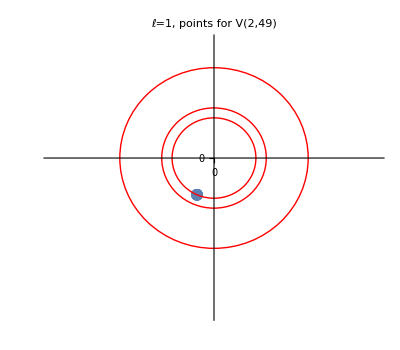

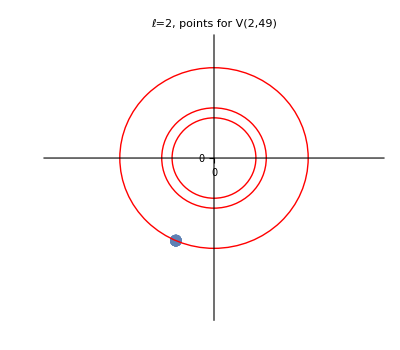

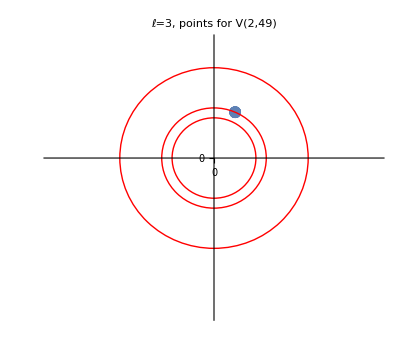

49 3 3 -1.07195-0.697765 ⅈ  0.859641+0.559564 ⅈ  -1.9316-1.25733 ⅈ  -20/49 9/98 -20/49

49 3 10 1.26855+0.163561 ⅈ  -1.0173-0.131166 ⅈ  2.28584+0.294727 ⅈ  1/49 -47/98 1/49

49 3 17 -1.21389+0.403039 ⅈ  0.973462-0.323212 ⅈ  -2.18735+0.72625 ⅈ  22/49 -5/98 22/49

49 3 24 0.918803-0.889811 ⅈ  -0.736823+0.713573 ⅈ  1.65563-1.60338 ⅈ  -6/49 37/98 -6/49

49 3 31 -0.441738+1.20035 ⅈ  0.354247-0.962603 ⅈ  -0.795985+2.16295 ⅈ  15/49 -19/98 15/49

49 3 38 -0.122818-1.27314 ⅈ  0.0984924+1.02098 ⅈ  -0.22131-2.29411 ⅈ  -13/49 23/98 -13/49

49 3 45 0.663049+1.09377 ⅈ  -0.531724-0.877134 ⅈ  1.19477+1.9709 ⅈ  8/49 -33/98 8/49

-Graphics-

-Graphics-

-Graphics-

49 4 4 -0.663049+1.09377 ⅈ  0.531724-0.877134 ⅈ  -1.19477+1.9709 ⅈ  33/98 -8/49 33/98

49 4 11 0.122818-1.27314 ⅈ  -0.0984924+1.02098 ⅈ  0.22131-2.29411 ⅈ  -23/98 13/49 -23/98

49 4 18 0.441738+1.20035 ⅈ  -0.354247-0.962603 ⅈ  0.795985+2.16295 ⅈ  19/98 -15/49 19/98

49 4 25 -0.918803-0.889811 ⅈ  0.736823+0.713573 ⅈ  -1.65563-1.60338 ⅈ  -37/98 6/49 -37/98

49 4 32 1.21389+0.403039 ⅈ  -0.973462-0.323212 ⅈ  2.18735+0.72625 ⅈ  5/98 -22/49 5/98

49 4 39 -1.26855+0.163561 ⅈ  1.0173-0.131166 ⅈ  -2.28584+0.294727 ⅈ  47/98 -1/49 47/98

49 4 46 1.07195-0.697765 ⅈ  -0.859641+0.559564 ⅈ  1.9316-1.25733 ⅈ  -9/98 20/49 -9/98

-Graphics-

-Graphics-

-Graphics-

49 5 5 0.415193-0.937928 ⅈ  0.93293-2.10751 ⅈ  -0.517737+1.16958 ⅈ  -9/49 -9/49 31/98

49 5 12 0.415193-0.937928 ⅈ  0.93293-2.10751 ⅈ  -0.517737+1.16958 ⅈ  -9/49 -9/49 31/98

49 5 19 0.415193-0.937928 ⅈ  0.93293-2.10751 ⅈ  -0.517737+1.16958 ⅈ  -9/49 -9/49 31/98

49 5 26 0.415193-0.937928 ⅈ  0.93293-2.10751 ⅈ  -0.517737+1.16958 ⅈ  -9/49 -9/49 31/98

49 5 33 0.415193-0.937928 ⅈ  0.93293-2.10751 ⅈ  -0.517737+1.16958 ⅈ  -9/49 -9/49 31/98

49 5 40 0.415193-0.937928 ⅈ  0.93293-2.10751 ⅈ  -0.517737+1.16958 ⅈ  -9/49 -9/49 31/98

49 5 47 0.415193-0.937928 ⅈ  0.93293-2.10751 ⅈ  -0.517737+1.16958 ⅈ  -9/49 -9/49 31/98

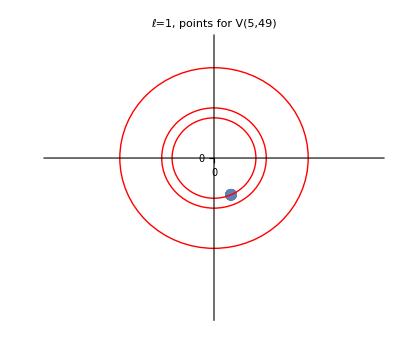

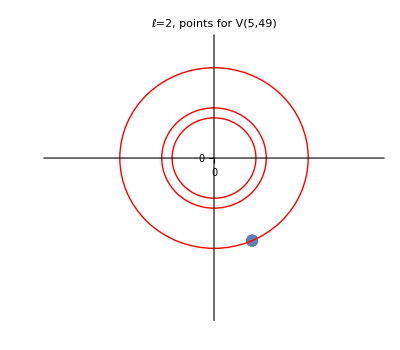

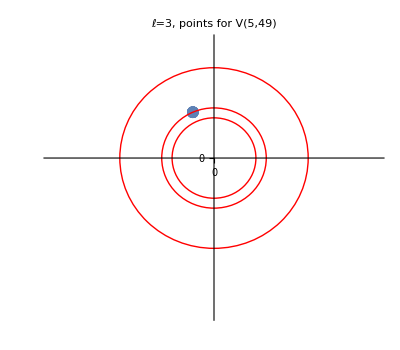

49 6 6 -1.19477-1.9709 ⅈ  -0.663049-1.09377 ⅈ  -0.531724-0.877134 ⅈ  -33/98 -33/98 -33/98

49 6 13 2.18735-0.72625 ⅈ  1.21389-0.403039 ⅈ  0.973462-0.323212 ⅈ  -5/98 -5/98 -5/98

49 6 20 0.22131+2.29411 ⅈ  0.122818+1.27314 ⅈ  0.0984924+1.02098 ⅈ  23/98 23/98 23/98

49 6 27 -2.28584-0.294727 ⅈ  -1.26855-0.163561 ⅈ  -1.0173-0.131166 ⅈ  -47/98 -47/98 -47/98

49 6 34 0.795985-2.16295 ⅈ  0.441738-1.20035 ⅈ  0.354247-0.962603 ⅈ  -19/98 -19/98 -19/98

49 6 41 1.9316+1.25733 ⅈ  1.07195+0.697765 ⅈ  0.859641+0.559564 ⅈ  9/98 9/98 9/98

49 6 48 -1.65563+1.60338 ⅈ  -0.918803+0.889811 ⅈ  -0.736823+0.713573 ⅈ  37/98 37/98 37/98

-Graphics-

-Graphics-

-Graphics-

98 1 1 2.13633+0.864902 ⅈ  1.18557+0.479985 ⅈ  0.950754+0.384918 ⅈ  3/49 3/49 3/49

98 1 15 -1.31859+1.8903 ⅈ  -0.731765+1.04904 ⅈ  -0.58683+0.841265 ⅈ  17/49 17/49 17/49

98 1 29 -1.5495-1.70617 ⅈ  -0.859905-0.946851 ⅈ  -0.68959-0.759316 ⅈ  -18/49 -18/49 -18/49

98 1 43 2.00818-1.13099 ⅈ  1.11446-0.627651 ⅈ  0.893726-0.503337 ⅈ  -4/49 -4/49 -4/49

98 1 57 0.655769+2.2095 ⅈ  0.363924+1.22618 ⅈ  0.291845+0.983322 ⅈ  10/49 10/49 10/49

98 1 71 -2.30003+0.147667 ⅈ  -1.27642+0.0819489 ⅈ  -1.02361+0.0657179 ⅈ  24/49 24/49 24/49

98 1 85 0.36784-2.27522 ⅈ  0.204136-1.26265 ⅈ  0.163704-1.01257 ⅈ  -11/49 -11/49 -11/49

-Graphics-

-Graphics-

-Graphics-

98 3 3 0.363924-1.22618 ⅈ  -0.291845+0.983322 ⅈ  0.655769-2.2095 ⅈ  -10/49 29/98 -10/49

98 3 17 0.204136+1.26265 ⅈ  -0.163704-1.01257 ⅈ  0.36784+2.27522 ⅈ  11/49 -27/98 11/49

98 3 31 -0.731765-1.04904 ⅈ  0.58683+0.841265 ⅈ  -1.31859-1.8903 ⅈ  -17/49 15/98 -17/49

98 3 45 1.11446+0.627651 ⅈ  -0.893726-0.503337 ⅈ  2.00818+1.13099 ⅈ  4/49 -41/98 4/49

98 3 59 -1.27642-0.0819489 ⅈ  1.02361+0.0657179 ⅈ  -2.30003-0.147667 ⅈ  -24/49 1/98 -24/49

98 3 73 1.18557-0.479985 ⅈ  -0.950754+0.384918 ⅈ  2.13633-0.864902 ⅈ  -3/49 43/98 -3/49

98 3 87 -0.859905+0.946851 ⅈ  0.68959-0.759316 ⅈ  -1.5495+1.70617 ⅈ  18/49 -13/98 18/49

-Graphics-

-Graphics-

-Graphics-

98 5 5 -0.859641+0.559564 ⅈ  -1.9316+1.25733 ⅈ  1.07195-0.697765 ⅈ  20/49 20/49 -9/98

98 5 19 -0.859641+0.559564 ⅈ  -1.9316+1.25733 ⅈ  1.07195-0.697765 ⅈ  20/49 20/49 -9/98

98 5 33 -0.859641+0.559564 ⅈ  -1.9316+1.25733 ⅈ  1.07195-0.697765 ⅈ  20/49 20/49 -9/98

98 5 47 -0.859641+0.559564 ⅈ  -1.9316+1.25733 ⅈ  1.07195-0.697765 ⅈ  20/49 20/49 -9/98

98 5 61 -0.859641+0.559564 ⅈ  -1.9316+1.25733 ⅈ  1.07195-0.697765 ⅈ  20/49 20/49 -9/98

98 5 75 -0.859641+0.559564 ⅈ  -1.9316+1.25733 ⅈ  1.07195-0.697765 ⅈ  20/49 20/49 -9/98

98 5 89 -0.859641+0.559564 ⅈ  -1.9316+1.25733 ⅈ  1.07195-0.697765 ⅈ  20/49 20/49 -9/98

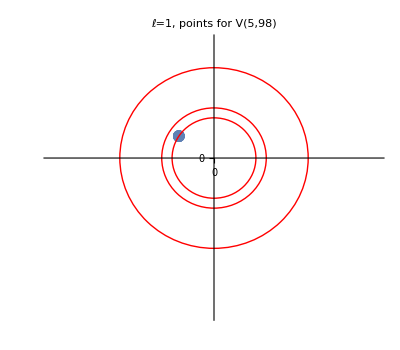

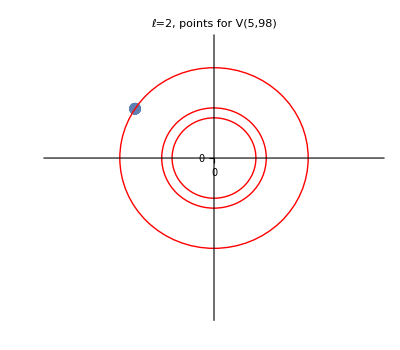

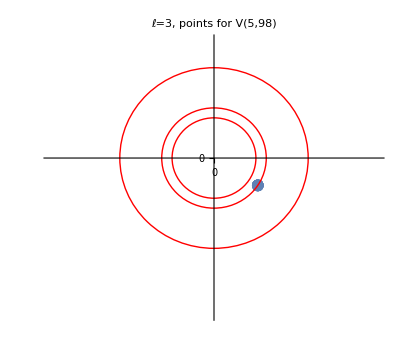

98 9 9 0.859641+0.559564 ⅈ  1.9316+1.25733 ⅈ  -1.07195-0.697765 ⅈ  9/98 9/98 -20/49

98 9 23 0.859641+0.559564 ⅈ  1.9316+1.25733 ⅈ  -1.07195-0.697765 ⅈ  9/98 9/98 -20/49

98 9 37 0.859641+0.559564 ⅈ  1.9316+1.25733 ⅈ  -1.07195-0.697765 ⅈ  9/98 9/98 -20/49

98 9 51 0.859641+0.559564 ⅈ  1.9316+1.25733 ⅈ  -1.07195-0.697765 ⅈ  9/98 9/98 -20/49

98 9 65 0.859641+0.559564 ⅈ  1.9316+1.25733 ⅈ  -1.07195-0.697765 ⅈ  9/98 9/98 -20/49

98 9 79 0.859641+0.559564 ⅈ  1.9316+1.25733 ⅈ  -1.07195-0.697765 ⅈ  9/98 9/98 -20/49

98 9 93 0.859641+0.559564 ⅈ  1.9316+1.25733 ⅈ  -1.07195-0.697765 ⅈ  9/98 9/98 -20/49

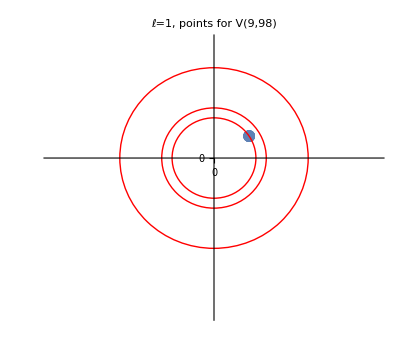

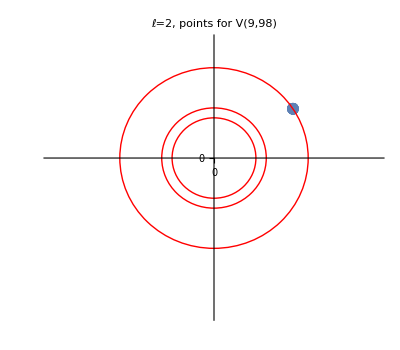

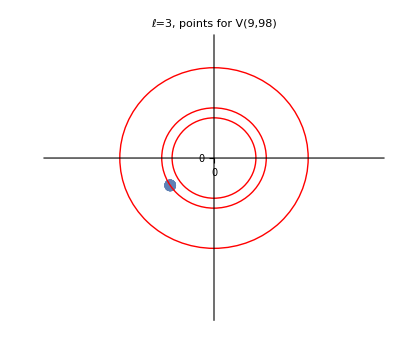

98 11 11 0.859905+0.946851 ⅈ  -0.68959-0.759316 ⅈ  1.5495+1.70617 ⅈ  13/98 -18/49 13/98

98 11 25 -1.18557-0.479985 ⅈ  0.950754+0.384918 ⅈ  -2.13633-0.864902 ⅈ  -43/98 3/49 -43/98

98 11 39 1.27642-0.0819489 ⅈ  -1.02361+0.0657179 ⅈ  2.30003-0.147667 ⅈ  -1/98 24/49 -1/98

98 11 53 -1.11446+0.627651 ⅈ  0.893726-0.503337 ⅈ  -2.00818+1.13099 ⅈ  41/98 -4/49 41/98

98 11 67 0.731765-1.04904 ⅈ  -0.58683+0.841265 ⅈ  1.31859-1.8903 ⅈ  -15/98 17/49 -15/98

98 11 81 -0.204136+1.26265 ⅈ  0.163704-1.01257 ⅈ  -0.36784+2.27522 ⅈ  27/98 -11/49 27/98

98 11 95 -0.363924-1.22618 ⅈ  0.291845+0.983322 ⅈ  -0.655769-2.2095 ⅈ  -29/98 10/49 -29/98

-Graphics-

-Graphics-

-Graphics-

98 13 13 -0.36784-2.27522 ⅈ  -0.204136-1.26265 ⅈ  -0.163704-1.01257 ⅈ  -27/98 -27/98 -27/98

98 13 27 2.30003+0.147667 ⅈ  1.27642+0.0819489 ⅈ  1.02361+0.0657179 ⅈ  1/98 1/98 1/98

98 13 41 -0.655769+2.2095 ⅈ  -0.363924+1.22618 ⅈ  -0.291845+0.983322 ⅈ  29/98 29/98 29/98

98 13 55 -2.00818-1.13099 ⅈ  -1.11446-0.627651 ⅈ  -0.893726-0.503337 ⅈ  -41/98 -41/98 -41/98

98 13 69 1.5495-1.70617 ⅈ  0.859905-0.946851 ⅈ  0.68959-0.759316 ⅈ  -13/98 -13/98 -13/98

98 13 83 1.31859+1.8903 ⅈ  0.731765+1.04904 ⅈ  0.58683+0.841265 ⅈ  15/98 15/98 15/98

98 13 97 -2.13633+0.864902 ⅈ  -1.18557+0.479985 ⅈ  -0.950754+0.384918 ⅈ  43/98 43/98 43/98

-Graphics-

-Graphics-

-Graphics-

```mathematica
p=7;NN=98;n=2;(*n=5 means 7n+5 case*)
For[c=0,c<=NN,c+=49,
If[True,
graphc={};cc=c/7;
For[r=1,r<=cc,r++,
If[GCD[r,cc]==1,
sd1=0;sd2=0;sd3=0;graphr1={};graphr2={};graphr3={};
For[d=1,d<=c,d++,
If[GCD[d,c]==1&&(Mod[d,cc]==r||cc==1),
a=ModularInverse[d,c];b=(a*d-1)/c;
Pdl1=N[Conjugate[mu[c,d,Mod[a*1,p],p]]/Sin[Pi*Mod[a*1,p]/p]*Exp[-Pi*I*s[d,c]]*Exp[2Pi*I*(n*d)/c]];
sd1+=Pdl1;(*AppendTo[graphr1,Pdl1->Style[StringForm["d_(`1`), d_1 `2`",Mod[d,5],Rationalize[doublebracket[Rationalize[Arg[Pdl1]/2/Pi]-Argl1M1+1/2]]],FontSize->14]]*);
AppendTo[graphr1,Pdl1->Style[d,FontSize->24]];
Pdl2=N[Conjugate[mu[c,d,Mod[a*2,p],p]]/Sin[Pi*Mod[a*2,p]/p]*Exp[-Pi*I*s[d,c]]*Exp[2Pi*I*(n*d)/c]];
sd2+=Pdl2;(*AppendTo[graphr2,Pdl2->Style[StringForm["d_(`1`), d_1 `2`",Mod[d,5],Rationalize[doublebracket[Rationalize[Arg[Pdl2]/2/Pi]-Argl2M1+1/2]]],FontSize->14]]*);
AppendTo[graphr2,Pdl2->Style[d,FontSize->24]];
Pdl3=N[Conjugate[mu[c,d,Mod[a*3,p],p]]/Sin[Pi*Mod[a*3,p]/p]*Exp[-Pi*I*s[d,c]]*Exp[2Pi*I*(n*d)/c]];
sd3+=Pdl3;(*AppendTo[graphr2,Pdl2->Style[StringForm["d_(`1`), d_1 `2`",Mod[d,5],Rationalize[doublebracket[Rationalize[Arg[Pdl2]/2/Pi]-Argl2M1+1/2]]],FontSize->14]]*);
AppendTo[graphr3,Pdl3->Style[d,FontSize->24]];
Print[c," ",r," ",d," ",Pdl1,"  ",Pdl2, "  ",Pdl3,"  ",Rationalize[Arg[Pdl1]/2/Pi]," ",Rationalize[Arg[Pdl2]/2/Pi]," ",Rationalize[Arg[Pdl3]/2/Pi]];
]
];

(*A=cc;beta=ModularInverse[A,7];betam=ModularInverse[-A,7];
If[beta==1||beta==2||beta==3,
For[sss=0,sss<=6,sss++,If[Mod[r+sss*A,7]==1,Rd1=r+sss*A]];
T=(A*beta-1)/7;
BB=-Rd1*T;
CC=-7*ModularInverse[Rd1,A];
Q1=(-1)^(7*T)*I*Sqrt[7];
Q21=Exp[2*Pi*I*(3/2*T^2+1/2*T)*CC/A];
Q22=Exp[-Pi*I*s[BB,A]];
Q2=Q21*Q22;
Q3=Exp[2*Pi*I*n*BB/A];
Qall=N[Q1*Q2*Q3];
Q1arg=Rationalize[Arg[Q1]/2/Pi];
Q21arg=Rationalize[Arg[Q21]/2/Pi];
Q22arg=Rationalize[Arg[Q22]/2/Pi];
Q2arg=Rationalize[Arg[Q2]/2/Pi];
Q3arg=Rationalize[Arg[Q3]/2/Pi];
Qarg=Rationalize[Arg[Qall]/2/Pi];

If[beta==1,Print[C7[4,6]*Sin[Pi/7]*2*Qall];AppendTo[graphr1,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
If[beta==2,Print[C7[6,2]*Sin[2Pi/7]*2*Qall];AppendTo[graphr2,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];If[beta==3,Print[C7[2,4]*Sin[3Pi/7]*2*Qall];AppendTo[graphr3,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
];

If[betam==1||betam==2||betam==3,
For[sss=0,sss<=6,sss++,If[Mod[r+sss*A,7]==1,Rd1=r+sss*A]];
T=(A*betam+1)/7;
BB=Rd1*T;
CC=-7*ModularInverse[Rd1,A];
Q1=(-1)^(7*T-7)*I*Sqrt[7];
Q21=Exp[2*Pi*I*(3/2*(T-1)^2+5/2*(T-1)+1)*CC/A];
Q22=Exp[-Pi*I*s[BB,A]];
Q2=Q21*Q22;
Q3=Exp[2*Pi*I*n*BB/A];
Qall=N[Q1*Q2*Q3];
Qarg=Rationalize[Arg[Qall]/2/Pi];
If[betam==1,Print[C7[4,6]*Sin[Pi/7]*2*Qall];AppendTo[graphr1,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
If[betam==2,Print[C7[6,2]*Sin[2Pi/7]*2*Qall];AppendTo[graphr2,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];If[betam==3,Print[C7[2,4]*Sin[3Pi/7]*2*Qall];AppendTo[graphr3,Qall->Style[StringForm["B=`1`",Mod[BB,A]],FontSize->24]]];
];

Print[sd1, "  ", sd2,"   ",sd3,"   ",Chop[C7[4,6]*Sin[Pi/7]*sd1+C7[6,2]*Sin[2Pi/7]*sd2+C7[2,4]*Sin[3Pi/7]*sd3]];
*);
Print[ComplexListPlot[graphr1,PlotStyle->{PointSize[Large]},PlotMarkers->{Automatic,12},AxesOrigin->{0,0},Ticks->{{{0,"0"}},{{0,"0"}}},LabelStyle->Style[FontFamily->"Times New Roman",FontSize->24],Epilog->{{Red,Circle[{0,0},1/Sin[Pi/p]]},{Red,Circle[{0,0},1/Sin[2*Pi/p]]} ,{Red,Circle[{0,0},1/Sin[3*Pi/p]]} },PlotRange->{{-4,4},{-4,3}},PlotLabel->Style[StringForm["ℓ=1, points for V(`1`,`2`)",r,c],FontSize->24]]];Print[ComplexListPlot[graphr2,PlotStyle->{PointSize[Large]},PlotMarkers->{Automatic,12},AxesOrigin->{0,0},Ticks->{{{0,"0"}},{{0,"0"}}},LabelStyle->Style[FontFamily->"Times New Roman",FontSize->24],Epilog->{{Red,Circle[{0,0},1/Sin[Pi/p]]},{Red,Circle[{0,0},1/Sin[2*Pi/p]]},{Red,Circle[{0,0},1/Sin[3*Pi/p]]}},PlotRange->{{-4,4},{-4,3}},PlotLabel->Style[StringForm["ℓ=2, points for V(`1`,`2`)",r,c],FontSize->24]]];
Print[ComplexListPlot[graphr3,PlotStyle->{PointSize[Large]},PlotMarkers->{Automatic,12},AxesOrigin->{0,0},Ticks->{{{0,"0"}},{{0,"0"}}},LabelStyle->Style[FontFamily->"Times New Roman",FontSize->24],Epilog->{{Red,Circle[{0,0},1/Sin[Pi/p]]},{Red,Circle[{0,0},1/Sin[2*Pi/p]]},{Red,Circle[{0,0},1/Sin[3*Pi/p]]}},PlotRange->{{-4,4},{-4,3}},PlotLabel->Style[StringForm["ℓ=3, points for V(`1`,`2`)",r,c],FontSize->24]]];
]
]
]
]
```